# Isotropic Tension

### data loading

```mathematica
p0s={3.85,3.825,3.80}
```

{3.85,3.825,3.8}

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022}};
 records=Table[Table[i,{i,10,14}],Length[p0s]];
epsilons={{-0.001,0.,0.001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.825/isoCompression/timePressue_isoCompression_N4096_p3.8250_T0.00800000_epsilon0.00000000_KA1.0000_KP0.0000_idx11.nc"]
```

{/firstValue,/secondValue}

```mathematica
timePressureArea=Table[
Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA1.0000_KP0.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],0.,records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.850/isoCompression/timePressue_isoCompression_N4096_p3.8500_T0.03900000_epsilon0.00000000_KA1.0000_KP0.0000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.850/isoCompression/timePressue_isoCompression_N4096_p3.8500_T0.01600000_epsilon0.00000000_KA1.0000_KP0.0000_idx12.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.850/isoCompression/timePressue_isoCompression_N4096_p3.8500_T0.01000000_epsilon0.00000000_KA1.0000_KP0.0000_idx12.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressurePeri=Table[
Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA0.0000_KP1.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],0.,records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.850/isoCompression/timePressue_isoCompression_N4096_p3.8500_T0.03900000_epsilon0.00000000_KA0.0000_KP1.0000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.850/isoCompression/timePressue_isoCompression_N4096_p3.8500_T0.01600000_epsilon0.00000000_KA0.0000_KP1.0000_idx12.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.850/isoCompression/timePressue_isoCompression_N4096_p3.8500_T0.01000000_epsilon0.00000000_KA0.0000_KP1.0000_idx12.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
meanPressurePeri=Table[
Table[Mean[Flatten[Table[Normal[timePressurePeri[[p,T,i,2]]],{i,Length[timePressurePeri[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.229592,0.116926,0.0766417,0.0374351,0.0277604,0.0163268,0.0122108,0.0047551,0.00180408,0.00104781,0.000760397,0.000387077,0.000237233,0.000205199,0.000151288,0.000118891,0.00009733},{0.362169,0.274202,0.237261,0.147961,0.100319,0.0818686,0.0649864,0.0511074,0.0383441,0.0296508,0.0227571,0.0167833,0.011012,0.00550615,0.00197178,0.000318563},{0.416181,0.321957,0.281911,0.246634,0.182329,0.125927,0.102793,0.0808574,0.0623245,0.0440458,0.0306125,0.0256476,0.0211969,0.0163676}}

```mathematica
meanPressureArea=Table[
Table[Mean[Flatten[Table[Normal[timePressureArea[[p,T,i,2]]],{i,Length[timePressurePeri[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0126411,0.00612195,0.00423503,0.00250684,0.00206582,0.00150069,0.00127045,0.000744039,0.000419181,0.000291457,0.000226764,0.00013215,0.0000874221,0.0000744121,0.0000526852,0.0000440271,0.0000353738},{0.0183945,0.0122812,0.0101335,0.00583114,0.00398234,0.00333417,0.00276689,0.00231553,0.00189759,0.00161173,0.00137095,0.00115847,0.000931781,0.000680778,0.000492296,0.000385159},{0.0180316,0.0119485,0.00981676,0.00814463,0.00555023,0.00371651,0.00307194,0.00250548,0.00205498,0.00163247,0.00133151,0.00121405,0.00110084,0.000979951}}

```mathematica
tension=meanPressureArea+meanPressurePeri
```

{{0.242233,0.123048,0.0808767,0.0399419,0.0298262,0.0178275,0.0134812,0.00549914,0.00222326,0.00133927,0.000987161,0.000519227,0.000324655,0.000279611,0.000203973,0.000162918,0.000132704},{0.380564,0.286483,0.247395,0.153792,0.104301,0.0852028,0.0677532,0.0534229,0.0402417,0.0312625,0.024128,0.0179418,0.0119438,0.00618693,0.00246407,0.000703722},{0.434213,0.333906,0.291728,0.254779,0.187879,0.129644,0.105865,0.0833628,0.0643794,0.0456783,0.031944,0.0268616,0.0222978,0.0173475}}

## compare with G_p

```mathematica
gp={{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031}};
```

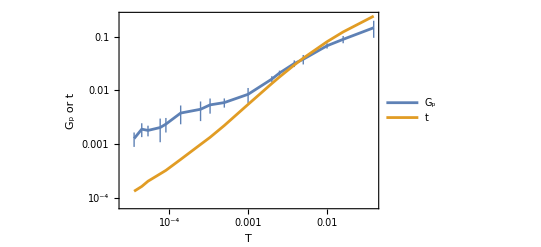
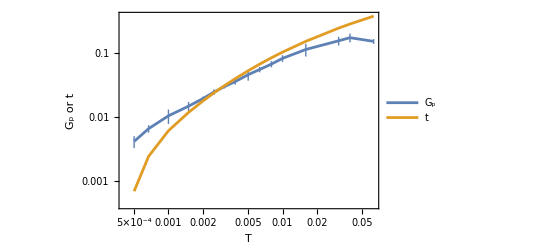
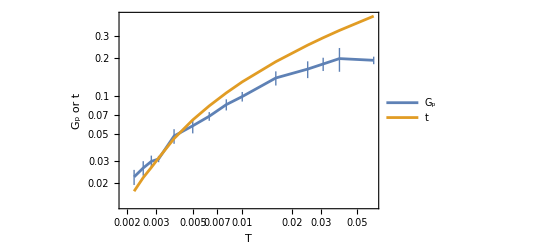

```mathematica
comparisionPLots=Table[ListLogLogPlot[{Table[{temperatures[[p,T]],gp[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],tension[[p,T]]},{T,Length[temperatures[[p]]]}]},Joined->True,ImageSize->400,PlotLegends->{"G_p","t"},FrameLabel->{"T ","G_p or t"}],{p,Length[p0s]}]
```

```mathematica
tauAlpha={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3}};
```

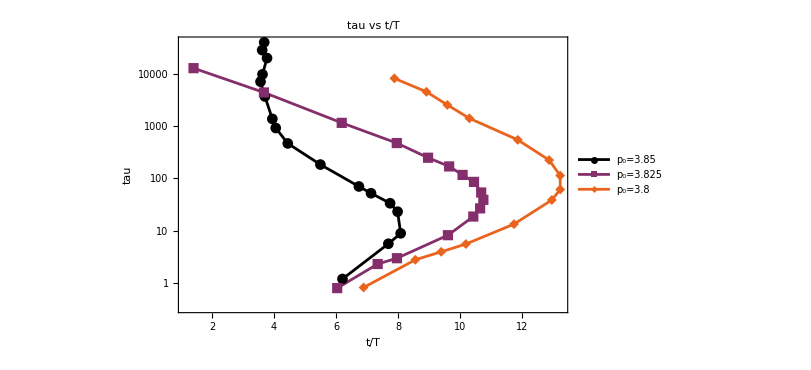

```mathematica
gpTPlot=Show[ListLogPlot[Table[Table[{tension[[p,T]]/temperatures[[p,T]],tauAlpha[[p,T,1]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->True,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]]]
```

```mathematica
Export["/home/chengling/Research/updates/07282024/gpandt.jpeg",Grid[Partition[comparisionPLots,1]],ImageResolution->300]
```

/home/chengling/Research/updates/07282024/gpandt.jpeg

```mathematica
Export["/home/chengling/Research/updates/07282024/tTscale.jpeg",gpTPlot,ImageResolution->300]
```

/home/chengling/Research/updates/07282024/tTscale.jpeg

## comparison with Matthais

```mathematica
tensionPrediction[kE_,kS_,p0_,p_,T_]:=1/2 kE(Log[p0/p]+Abs[Log[p0/p]]*Sqrt[1+(4kS T)/(kE Log[p0/p])^2]);
```

```mathematica
gPrediction[kE_,kS_,p0_,b_,p_,T_]:=4b*1/2 kE(Log[p0/p]+Abs[Log[p0/p]]*Sqrt[1+(4kS T)/(kE Log[p0/p])^2]);
```

```mathematica
fittings=Table[NonlinearModelFit[Table[{temperatures[[p,T]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{tensionPrediction[kE,kS,p0,p0s[[p]],T],{p0>2}},{kE,kS,p0},T],{p,Length[p0s]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
fittings[[2]]["BestFitParameters"]
```

{kE→3.45672,kS→4.55543,p0→3.45773}

```mathematica
fittings[[3]]["BestFitParameters"]
```

{kE→3.41216,kS→5.65304,p0→3.43968}

```mathematica
fittings[[1]]["BestFitParameters"]
```

{kE→1.96497,kS→5.04661,p0→2.88991}

```mathematica
Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],1]
```

{{0.039,3.85,0.242233},{0.016,3.85,0.123048},{0.01,3.85,0.0808767},{0.005,3.85,0.0399419},{0.00385,3.85,0.0298262},{0.0025,3.85,0.0178275},{0.002,3.85,0.0134812},{0.001,3.85,0.00549914},{0.0005,3.85,0.00222326},{0.00033,3.85,0.00133927},{0.00025,3.85,0.000987161},{0.00014,3.85,0.000519227},{0.000091,3.85,0.000324655},{0.000077,3.85,0.000279611},{0.000054,3.85,0.000203973},{0.000045,3.85,0.000162918},{0.000036,3.85,0.000132704},{0.063,3.825,0.380564},{0.039,3.825,0.286483},{0.03105,3.825,0.247395},{0.016,3.825,0.153792},{0.01,3.825,0.104301},{0.008,3.825,0.0852028},{0.0063,3.825,0.0677532},{0.005,3.825,0.0534229},{0.00385,3.825,0.0402417},{0.0031,3.825,0.0312625},{0.0025,3.825,0.024128},{0.002,3.825,0.0179418},{0.0015,3.825,0.0119438},{0.001,3.825,0.00618693},{0.00067,3.825,0.00246407},{0.0005,3.825,0.000703722},{0.063,3.8,0.434213},{0.039,3.8,0.333906},{0.03105,3.8,0.291728},{0.025,3.8,0.254779},{0.016,3.8,0.187879},{0.01,3.8,0.129644},{0.008,3.8,0.105865},{0.0063,3.8,0.0833628},{0.005,3.8,0.0643794},{0.00385,3.8,0.0456783},{0.0031,3.8,0.031944},{0.0028,3.8,0.0268616},{0.0025,3.8,0.0222978},{0.0022,3.8,0.0173475}}

```mathematica
fitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}],1],{tensionPrediction[kE,kS,p0,p,T],{p0>2}},{kE,kS,p0},{T,p}]
```

FittedModel[…]

```mathematica
fitting["BestFitParameters"]
```

{kE→22.2103,kS→5.29403,p0→3.74866}

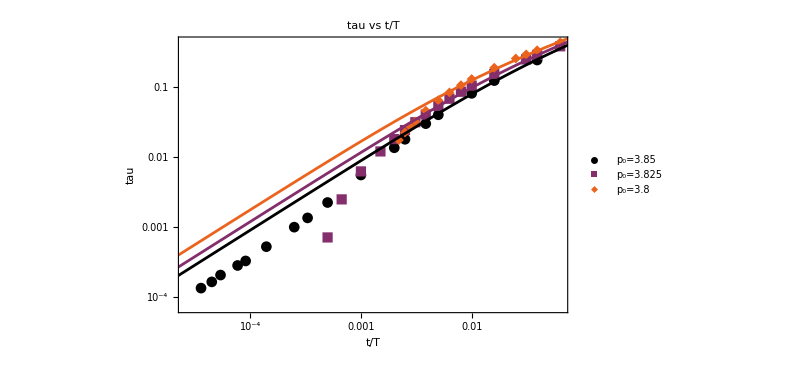

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],tension[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[fitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->gradientColScheme[5][[p]]],{p,Length[p0s]}]]
```

```mathematica
gfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],gp[[p,T]]},{T,{Length[temperatures[[p]]],Length[temperatures[[p]]],9}[[p]]}],{p,Length[p0s]}],1],{gPrediction[kE,kS,p0,b,p,T],{p0>3,100>kE>1,100>kS>1}},{kE,kS,p0,b},{T,p}]
```

FittedModel[…]

```mathematica
gfitting["BestFitParameters"]
```

{kE→14.2035,kS→9.44582,p0→3.7708,b→0.0772224}

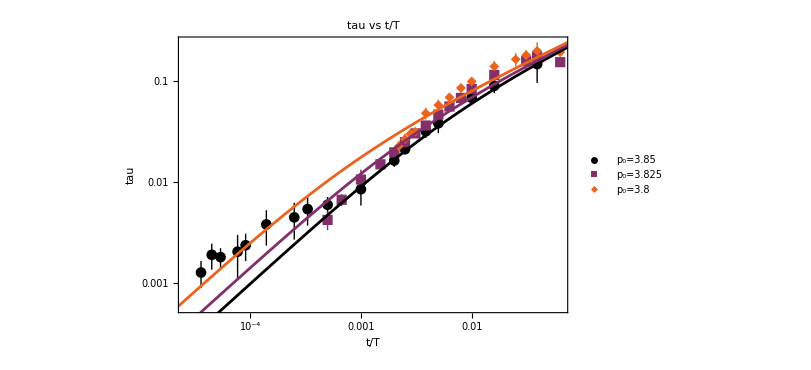

```mathematica
Show[ListLogLogPlot[Table[Table[{temperatures[[p,T]],gp[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLogPlot[gfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->gradientColScheme[5][[p]]],{p,Length[p0s]}]]
```

```mathematica
bulkmodulusPeri={{3.1327868264012793,2.146669679594135,1.625445274825759,0.9613447767457817,0.7708497810237818,0.49584760259221594,0.3896030453314479,0.14924549774367601,0.045367576364034615,0.017862914323601802,0.013366041456455355,0.00727435539984978,0.008808819267151232,0.007044538150156038,0.008378659397645332,0.009381521318033909,0.004916821772182463},{3.9235712490701955,3.34492964624597,3.1090866508401844,2.394355999351477,1.81350140799965,1.5372789312579487,1.2562339007358252,1.0098889800876314,0.697893661877171,0.5144012690755295,0.31436160117244083,0.16183413459527374,0.05992257043973409,-0.1895833548666876,-0.37799115694107793,-0.2784861412942186},{3.9845466836681,3.5530111069355526,3.3680861484574054,3.092336863122748,2.56849555108396,1.7945904545591598,1.3708111421703097,0.8165136813594182,0.28331545146936116,-0.23555257510001448,-0.5267191387567112,-0.4692168330328048,-0.23833051629748753,-0.1305220947298187}};
```

```mathematica
kfitting=NonlinearModelFit[Flatten[Table[Table[{temperatures[[p,T]],p0s[[p]],bulkmodulusPeri[[p,T]]},{T,{Length[temperatures[[p]]],Length[temperatures[[p]]],9}[[p]]}],{p,Length[p0s]}],1],{gPrediction[kE,kS,p0,b,p,T],{p0>3,100>kE>1,100>kS>1}},{kE,kS,p0,b},{T,p}]
```

FittedModel[…]

```mathematica
kfitting["BestFitParameters"]
```

{kE→1.96559,kS→1.83329,p0→3.67329,b→3.65116}

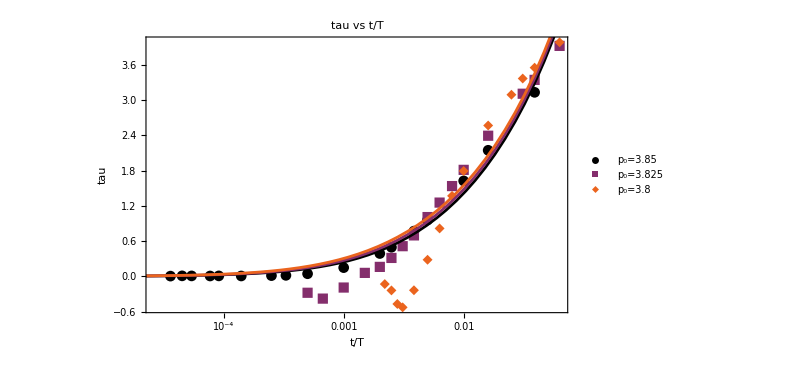

```mathematica
Show[ListLogLinearPlot[Table[Table[{temperatures[[p,T]],bulkmodulusPeri[[p,T]]},{T,Length[temperatures[[p]]]}],{p,3}],PlotStyle->gradientColScheme[5],FrameLabel->{"t/T ","tau"},ImageSize->600,PlotMarkers->Automatic,PlotLabel->"tau vs t/T",PlotRange->{All,All},Joined->False,PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}]],Table[LogLinearPlot[kfitting[T,p0s[[p]]],{T,0.00001,0.1},PlotStyle->gradientColScheme[5][[p]]],{p,Length[p0s]}]]
```